Demo: Kitaev Chain |

Spectral Propertiespaclet:Q3/tutorial/DemoKitaevChain#283481385 | Majorana Representationpaclet:Q3/tutorial/DemoKitaevChain#399500441

The Kitaev chain is a prototype example of the topological superconductor. Here, we demonstrate how to examine its properties using Q3. See Kitaev (2001), Kitaev's original, for technical details of the model.

FockNumberpaclet:Q3/ref/FockNumberQ3 Package Symbol or Qpaclet:Q3/ref/QQ3 Package Symbol | Number operator
FockHoppingpaclet:Q3/ref/FockHoppingQ3 Package Symbol or Hoppaclet:Q3/ref/HopQ3 Package Symbol | Constructs the hopping Hamiltonian terms
FockPairingpaclet:Q3/ref/FockPairingQ3 Package Symbol or Pairpaclet:Q3/ref/PairQ3 Package Symbol | Constructs the pairing Hamiltonian terms

Some useful functions to study the Kitaev chain.

Load Q3.

```mathematica
<<Q3`
```

Let c denote the (Dirac) Fermionpaclet:Q3/ref/FermionQ3 Package Symbol operator.

```mathematica
Let[Fermion,c]
```

Let t, μ, and Δ denote the hopping amplitude, chemical potential, and pairing potential, respectively.

```mathematica
Let[Real,t,μ,Δ]
```

The number of sites in the one-dimensional lattice.

```mathematica
$L=8;
```

Define some Lists of operators to be used later.

```mathematica
cc=c[Range[1,$L]]
cccc=Join[cc,Dagger@cc]
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,6),c_(,,7),c_(,,8)}

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,6),c_(,,7),c_(,,8),c_(,,1)^(,,†),c_(,,2)^(,,†),c_(,,3)^(,,†),c_(,,4)^(,,†),c_(,,5)^(,,†),c_(,,6)^(,,†),c_(,,7)^(,,†),c_(,,8)^(,,†)}

Now, constructs the model Hamiltonian.

```mathematica
H0=-μ*Q[cc]
Hhop=-t*PlusDagger @ FockHopping[cc]
Hpair=Δ*PlusDagger @ FockPairing[cc]
Htotal=H0+Hhop+Hpair
```

-μ (c_(,,1)^(,,†)c_(,,1)+c_(,,2)^(,,†)c_(,,2)+c_(,,3)^(,,†)c_(,,3)+c_(,,4)^(,,†)c_(,,4)+c_(,,5)^(,,†)c_(,,5)+c_(,,6)^(,,†)c_(,,6)+c_(,,7)^(,,†)c_(,,7)+c_(,,8)^(,,†)c_(,,8))

-Graphics-

-Graphics-

-Graphics-

Let us take a look at the connectivity of the model. Here, the black thin lines indicate single-particle tunneling and the red thick lines represent the p-wave pairing.

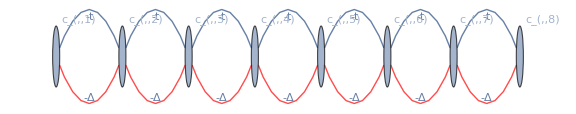

```mathematica
GraphForm[Htotal]
```

## Spectral Properties

To investigate the quasi-particle spectrum (by means of the Bogoliubov-de Gennes equation), obtain the single-particle BdG Hamiltonian.

```mathematica
matK=CoefficientTensor[Htotal,Dagger@cccc,cccc];
matK//MatrixForm
```

(-μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | 0
-t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0
0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0
0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0
0 | 0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0
0 | 0 | 0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0
0 | 0 | 0 | 0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2
0 | 0 | 0 | 0 | 0 | 0 | -t/2 | -μ/2 | 0 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0
0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | μ/2 | t/2 | 0 | 0 | 0 | 0 | 0 | 0
-Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0 | 0 | 0 | 0
0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0 | 0 | 0
0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0 | 0
0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0
0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0
0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2
0 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2)

Now, study the quasi-particle energy spectrum of the model. Be aware of the finite size effects.

```mathematica
KK[a_,b_,c_]:=Block[{μ=a,t=b,Δ=c},SparseArray@ArrayRules@matK]
```

```mathematica
Manipulate[
Module[
{eval=Table[Sort@Eigenvalues[KK[μ,1.,Δ]],{μ,0,4,0.02}]},
ListLinePlot[Transpose@eval,
Axes->None,
Frame->True,
FrameLabel->{"μ / t","Eenergy / t"},
DataRange->{0,4}]
],
{{Δ,1},0.5,2,0.1},
SaveDefinitions->True]
```

## Majorana Representation

```mathematica
Let[Majorana,a]
```

```mathematica
aa=a@Range[2*$L]
```

{a_(,,1),a_(,,2),a_(,,3),a_(,,4),a_(,,5),a_(,,6),a_(,,7),a_(,,8),a_(,,9),a_(,,10),a_(,,11),a_(,,12),a_(,,13),a_(,,14),a_(,,15),a_(,,16)}

```mathematica
Hmajor=ToMajorana[Htotal,cc->aa]
```

-4 μ-1/2 ⅈ μ a_(,,1)a_(,,2)-1/2 ⅈ (t-Δ) a_(,,1)a_(,,4)+1/2 ⅈ (t+Δ) a_(,,2)a_(,,3)-1/2 ⅈ μ a_(,,3)a_(,,4)-1/2 ⅈ (t-Δ) a_(,,3)a_(,,6)+1/2 ⅈ (t+Δ) a_(,,4)a_(,,5)-1/2 ⅈ μ a_(,,5)a_(,,6)-1/2 ⅈ (t-Δ) a_(,,5)a_(,,8)+1/2 ⅈ (t+Δ) a_(,,6)a_(,,7)-1/2 ⅈ μ a_(,,7)a_(,,8)-1/2 ⅈ (t-Δ) a_(,,7)a_(,,10)+1/2 ⅈ (t+Δ) a_(,,8)a_(,,9)-1/2 ⅈ μ a_(,,9)a_(,,10)-1/2 ⅈ (t-Δ) a_(,,9)a_(,,12)+1/2 ⅈ (t+Δ) a_(,,10)a_(,,11)-1/2 ⅈ μ a_(,,11)a_(,,12)-1/2 ⅈ (t-Δ) a_(,,11)a_(,,14)+1/2 ⅈ (t+Δ) a_(,,12)a_(,,13)-1/2 ⅈ μ a_(,,13)a_(,,14)-1/2 ⅈ (t-Δ) a_(,,13)a_(,,16)+1/2 ⅈ (t+Δ) a_(,,14)a_(,,15)-1/2 ⅈ μ a_(,,15)a_(,,16)

Let us consider a special case: t=Δ.

```mathematica
Hspecial=Block[
{Δ=t},
Hmajor
]
```

-4 μ-1/2 ⅈ μ a_(,,1)a_(,,2)+ⅈ t a_(,,2)a_(,,3)-1/2 ⅈ μ a_(,,3)a_(,,4)+ⅈ t a_(,,4)a_(,,5)-1/2 ⅈ μ a_(,,5)a_(,,6)+ⅈ t a_(,,6)a_(,,7)-1/2 ⅈ μ a_(,,7)a_(,,8)+ⅈ t a_(,,8)a_(,,9)-1/2 ⅈ μ a_(,,9)a_(,,10)+ⅈ t a_(,,10)a_(,,11)-1/2 ⅈ μ a_(,,11)a_(,,12)+ⅈ t a_(,,12)a_(,,13)-1/2 ⅈ μ a_(,,13)a_(,,14)+ⅈ t a_(,,14)a_(,,15)-1/2 ⅈ μ a_(,,15)a_(,,16)

Examine the connectivity.

```mathematica
matM=CoefficientTensor[Hspecial,aa,aa];
matM//MatrixForm
```

(0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0)

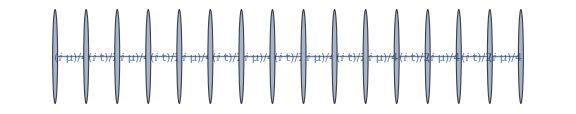

```mathematica
GraphForm[matM,VertexLabels->None]
```

This demonstrates that for 2|t|>|μ|, there exists two Majorana modes each localized at one of the two ends of the chain.

| Related Guides
▪Quantum Many-Body Systems

| Related Tech Notes
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪A. Kitaev, Physics-Uspekhi 44, 131 (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, "Unpaired Majorana fermions in quantum wires".
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).